# Data is Everywhere

## But you might have to squint to see it

### Mike Gallaher pragsmike@gmail.com

You can find data in places you didn’t expect, though sometimes you have to
squint a little, and it doesn’t have to be big to be interesting. In this talk
I’ll show how sound can be extracted from a 2D image of an oscillogram trace
printed in an old magazine article. This is an example of what Patrick Feaster
calls “educed audio”, where audio is derived from representations of sounds
that were not intended to be played, such as photographs of phonograph records.

## Examples of Found Data

Some data was never meant to be recognized or interpreted, but we can extract it anyway

### Educed Audio

popularized by Patrick Feaster; see Pictures of Sound

from pictures of waveforms in magazines

from photographs of phonograph records

### Data Modulated in Audio

Morse Code in songs, movies, games

HF Radio Packets in movie soundtrack

### Data Modulated in Video

The Famous Potato Chip Bag

## The Waveform in the Magazine

From a Nov 1923 Popular Science article on telephony, The Great American Voice by R. W. King, editor Bell System Technical Journal.
The article includes a reproduction of an oscillograph trace, originally 3 feet long, rendered as two strips each as wide as a page.

#### Page One

```mathematica
getimage[filename_]:=ColorConvert[Import[filename],GrayLevel];
page1=getimage["/home/mg/Documents/oscillograph/page68.jpg"];
page2=getimage["/home/mg/Documents/oscillograph/page69.jpg"];
page1
```

-Graphics-

## The Waveform in the Magazine

### Page Two

```mathematica
page2
```

-Graphics-

## The Waveform in the Magazine

### The Question: Is this really someone saying “America”?

Much information has been lost, so it won’t sound very good, but we should be able to at least tell whether it’s “America” or not.

### The raw input

Here’s the picture of the waveform clipped from the image and stitched together from the pieces.

```mathematica
snip[pageImage_,x_,y_,w_,h_]:=Block[{},
{pageWidth,pageHeight}=ImageDimensions[pageImage];
ImageTake[pageImage,{pageHeight-(y+h),pageHeight-y},{x,x+w}]
];
spec1={page1,78,1607,1144,175};
spec2={page2,20,1571,1145,175};
strip1=snip@@ spec1;
strip2=snip@@spec2;
strip =ImageAssemble[{strip1,strip2}]
```

-Graphics-

```mathematica
Import["/home/mg/Documents/oscillograph/signal-coarse.png"]
```

-Graphics-

Our strategy will take advantage of the fact that the original oscillograph trace
is truly a single-valued function, because the beam scans left to right and never
“doubles back” to the left.  That means that for each instant of time,
the trace has exactly one scalar value.

Our task then is to extract that scalar value for each time instant.

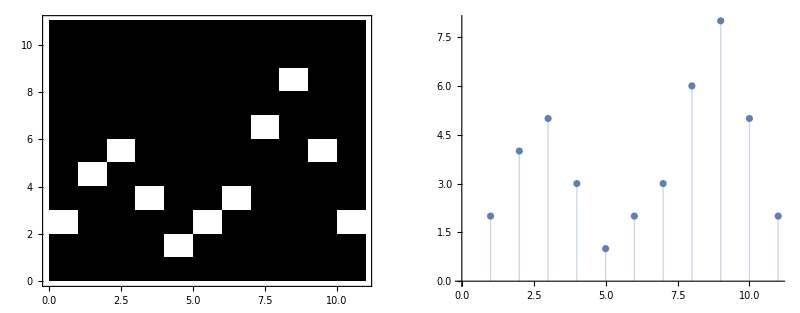

```mathematica
s={2,4,5,3,1,2,3,6,8,5,2};
r[x_,y_]:=s[[y+1]]==x;
ras=Raster[Table[If[r[x,y],1,0],{x,0,10},{y,0,10}]];
GraphicsRow[{Graphics[ras,Frame->True],ListPlot[s,Filling->Axis] }]
```

## The Waveform in the Magazine

First let’s crop the image to isolate just the waveform part.

```mathematica
rstrip1=ImageTake[strip1,{42,168},{30,1144}];
rstrip2=ImageTake[strip2,{42,168},{5,1139}];
rstrip=ImageAssemble[{rstrip1,rstrip2}]
```

-Graphics-

Here’s a magnified view of the first part of that image:

```mathematica
col=ImageData @ ImageTake[rstrip,{0,ImageDimensions[rstrip][[2]]}, {0,30}];
Graphics [Scale[Raster[col],{100,20}]]
```

-Graphics-

The first column does in fact show a sharp peak that’s obviously the position of the trace.

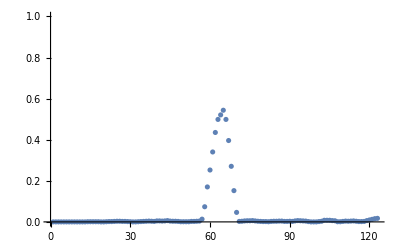

```mathematica
in=1;ListPlot[{MovingAverage[vertStrip[[in]],5]},PlotRange->1.0]
```

But we don’t have to look far to find a column where it’s not so obvious:

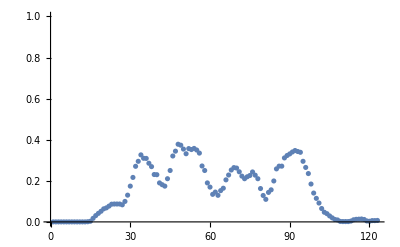

```mathematica
in=57;ListPlot[{MovingAverage[vertStrip[[in]],5]},PlotRange->1.0]
```

Here’s an interactive way to explore the image column-by-column:

```mathematica
Manipulate[
p = ListPlot[{MovingAverage[vertStrip[[in]],5]},PlotRange->1.0];
col=ImageData @ ImageTake[rstrip,{0,ImageDimensions[rstrip][[2]]}, {in,in}];
s =Graphics @ Scale[Raster[col],{80,1}];
GraphicsRow[{s,p}],
{in,1,Length[vertStrip],1}]
```

## The Waveform in the Magazine

### Distortion from halftone and undersampling

The problem is that we’re not working with the original oscillograph.  We have an imperfect rendering
of it that has been printed via a halftone process and then scanned (by Google).  The halftone
process reduces spatial resolution, to get better resolution of intensity (gray values).

Furthermore, the article says the oscillograph can resolve frequencies up to about 2000 Hz,
so we’d have to sample at 4000 Hz to avoid aliasing.  The image is around 2200 pixels wide,
and the utterance is about one second, so our sampling frequency is around 2500 Hz -- not
much greater than the maximum signal frequency, and much less than 4000 Hz.

Therefore, we may find that each row doesn’t have a single peak, because the signal
from successive instants may have been smeared by halftoning and aliased due to undersampling.

## The Waveform in the Magazine

### Finally, the audio!

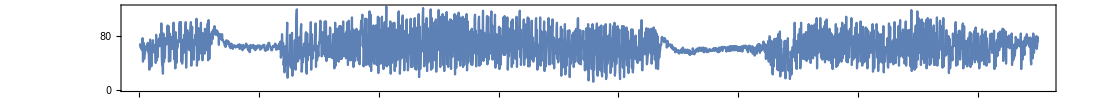

```mathematica
whereMax[x_]:=Position[x,Max[x]][[1]][[1]];
sigg[cols_]:=Array[whereMax[MovingAverage[cols[[#]],2]] &,Length[cols]];
astrip=ImageAdjust[rstrip,{0,0,2}];
vertStrip=Transpose[ImageData[astrip]];
signal=sigg[vertStrip];
ListPlot[signal,ImageSize->{1100,100},Frame->True,AspectRatio->Automatic,Joined->True]
```

```mathematica
ListPlay[signal,SampleRate->2500]
```

-Graphics-

Recovered

## Data Modulated in Audio

### Morse Code in music: B-52’s Planet Claire

This is from a Canadian marine weather station CFH, which sent weather reports periodically.  
Between bulletins, it repeated the sequence heard in the song.
In those days (up until early 1990s) the transmissions were in Morse code.
Nowadays, the station sends them in a format known as STANAG.

NAWS DE CFH II ZKR F1394

## Data Modulated in Audio

### Morse Code in music: Mike Oldfield Tubular Bells

This was (presumably) an unintentional inclusion.  This album was recorded in 1973 in England,
not far from a VLF radio station GBR which operated at 16 kHz.  This happens
to be in the audio range, and leaked into the studio equipment somehow.

Here’s a nice video that demonstrates extracting the signal using an SDR program.

Alan Cordwell offers this theory about how the signal might have been introduced:

Tubular Bells was recorded in late 1972 and early 1973 at The Manor Studio, Shipton on Cherwell. 
This is about 35 miles from Rugby -- not exactly on the back doorstep. 
There is no evidence of hum on the recordings so general poor shielding of a cable for example is unlikely. 
In my view, it could have been a playback head or dynamic mic whose coil just happened to be resonant at 16kHz. 
It would be interesting to find other recordings made at Manor and see if they also have this signal present on them.

## Data Modulated in Audio

AX.25 Packet in Movie Soundtrack: Star Trek IV

How Bob McGwier used a Cray 2 to decode a ham radio transmission heard in Star Trek IV

After decoding the noisy FSK signal to yield a binary NRZI-encoded bits, Bob says:

I took the bits to Phil Karn, KA9Q and he decoded the NRZI data and proved beyond a shadow of a doubt that 
it was indeed an HF amateur radio packet.

It was WA8ZCN-0 sending an RR for NR-3 to N6AEZ on 20 meters.

I got Bill Harrigill, WA8ZCN on the phone and he agrees that it was probably him.

## Data in Video

### The Famous Potato Chip Bag

Researchers at MIT, Microsoft, and Adobe have developed an algorithm that can reconstruct an audio signal 
by analyzing minute vibrations of objects depicted in video. 
In one set of experiments, they were able to recover intelligible speech from the vibrations of a potato-chip bag 
photographed from 15 feet away through soundproof glass. [emphasis mine]

## Data in Video

### Amplifying Invisible Video

MIT’s Computer Science and Artificial Intelligence Laboratory (CSAIL)